# PRACTICA 2 - 2

## ACTIVIDAD 1

### Implemente un módulo en Mathematica que, tomando como entrada un AFD proporcione como salida un AC unidireccional unidimensional que acepte el mismo lenguaje que el AFD mediante entrada paralela.

```mathematica
A1[A_]:=Module[{S,simbolos,transition,q0,Sf,f,i,j},
S=A[[1]];
simbolos=A[[2]];
transition=A[[3]];
q0=A[[4]];
Sf=A[[5]];
f={};

For[i=1,i≤Length[simbolos],i++,
For[j=1,j≤ Length[simbolos],j++,
AppendTo[f,{simbolos[[i]],simbolos[[j]],simbolos[[j]]}];
];
];

For[i=1,i≤ Length[S],i++,
For[j=1,j≤ Length[S],j++,
AppendTo[f,{S[[i]],S[[j]],S[[j]]}];
];
];

For[i=1,i≤ Length[transition],i++,
AppendTo[f,transition[[i]]];
];
Return[{S,f,Sf}];
];
```

```mathematica
ejemplo = { {q, p, r}, {a, b}, { {q, a, p}, {q, b, r}, {p, b, q}, {p, a, r}, {r, a, r}, {r, b ,r} }, q, {r} }
```

```mathematica
A1[ejemplo]
```

{{q,p,r},{{a,a,a},{a,b,b},{b,a,a},{b,b,b},{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{q,a,p},{q,b,r},{p,b,q},{p,a,r},{r,a,r},{r,b,r}},{r}}

## ACTIVIDAD 2

### Implemente un módulo Mathematica que, tomando como entrada una cadena arbitraria, un AC que reconoce un lenguaje mediante entrada paralela en tiempo real y un estado de frontera q pertenece a S, proporcione como salida True si el AC acepta la cadena y False en caso contrario.

```mathematica
A2[cadena_,AC_]:=Module[{S,transition,Sf,dir,actual,der,next,i,j,posDer},

S=AC[[1]];
transition=AC[[2]];
Sf=AC[[3]];

(* Comprobamos si es de tipo unidireccional o bidireccional *)
If[Length[transition[[1]]]==3,dir=True,dir=False];

actual = q;
der=transition[[1,2]];

For[i=1,i≤Length[cadena],i++,
posDer=i+1;
If[posDer>Length[cadena],posDer=i];
der=cadena[[posDer]];

If[dir,next=Cases[transition,{actual,cadena[[i]],_}],
next=Cases[transition,{actual,cadena[[i]],der,_}];
];
If[Length[next]==0,Return[False]];

If[dir,
actual=next[[1,3]],
actual=next[[1,4]];
];
];
If[MemberQ[Sf,actual]==False,Return[False]];

Return [True];

];
```

```mathematica
A2[
{a,b,a,a,b},
{
{q,p,r},
{{a,a,a,a},{a,a,b,a},{a,b,a,b},{a,b,b,b},{b,a,a,a},{b,a,b,a},{b,b,a,b},{b,b,b,b},{q,q,q,q},{q,q,p,q},{q,q,r,q},{q,p,q,p},{q,p,p,p},{q,p,r,p},{q,r,q,r},{q,r,p,r},{q,r,r,r},{p,q,q,q},{p,q,p,q},{p,q,r,q},{p,p,q,p},{p,p,p,p},{p,p,r,p},{p,r,q,r},{p,r,p,r},{p,r,r,r},{r,q,q,q},{r,q,p,q},{r,q,r,q},{r,p,q,p},{r,p,p,p},{r,p,r,p},{r,r,q,r},{r,r,p,r},{r,r,r,r},{q,a,a,p},{q,a,b,p},{q,b,a,r},{q,b,b,r},{p,b,a,q},{p,b,b,q},{p,a,a,r},{p,a,b,r},{r,a,a,r},{r,a,b,r},{r,b,a,r},{r,b,b,r}},
{r}
}
]
```

True

## ACTIVIDAD 3

### Proporcione una construcción formal para obtener a partir de un AFD, un AC equivalente unidimensional bidireccional (vecindario {-1,0,1}) con entrada paralela. Implemente un módulo en Mathematica que lleve a cabo la construcción propuesta.

```mathematica
A3[AFD_]:=Module[{S,simbolos,transition,q0,Sf,f,i,j,k},
S=AFD[[1]];
simbolos=AFD[[2]];
transition=AFD[[3]];
q0=AFD[[4]];
Sf=AFD[[5]];
f={};

For[i=1,i≤ Length[simbolos],i++,
For[j=1,j≤ Length[simbolos],j++,
For[k=1,k≤ Length[simbolos],k++,
AppendTo[f,{simbolos[[i]],simbolos[[j]],simbolos[[k]],simbolos[[j]]}];
];
];
];

For[i=1,i≤ Length[S],i++,
For[j=1,j≤ Length[S],j++,
For[k=1,k≤ Length[S],k++,
AppendTo[f,{S[[i]],S[[j]],S[[k]],S[[j]]}];
];
];
];

For[i=1,i≤ Length[transition],i++,
For[j=1,j≤ Length[simbolos],j++,
AppendTo[ f, {transition[[i,1]], transition[[i,2]], simbolos[[j]], transition[[i,3]]} ];
];
];

Return[{S,f,Sf}];
];
```

```mathematica
A3[
{ {q, p, r},
{a, b},
{ {q, a, p}, {q, b, r}, {p, b, q}, {p, a, r}, {r, a, r}, {r, b ,r} },
q,
{r} }
]
```

{{q,p,r},{{a,a,a,a},{a,a,b,a},{a,b,a,b},{a,b,b,b},{b,a,a,a},{b,a,b,a},{b,b,a,b},{b,b,b,b},{q,q,q,q},{q,q,p,q},{q,q,r,q},{q,p,q,p},{q,p,p,p},{q,p,r,p},{q,r,q,r},{q,r,p,r},{q,r,r,r},{p,q,q,q},{p,q,p,q},{p,q,r,q},{p,p,q,p},{p,p,p,p},{p,p,r,p},{p,r,q,r},{p,r,p,r},{p,r,r,r},{r,q,q,q},{r,q,p,q},{r,q,r,q},{r,p,q,p},{r,p,p,p},{r,p,r,p},{r,r,q,r},{r,r,p,r},{r,r,r,r},{q,a,a,p},{q,a,b,p},{q,b,a,r},{q,b,b,r},{p,b,a,q},{p,b,b,q},{p,a,a,r},{p,a,b,r},{r,a,a,r},{r,a,b,r},{r,b,a,r},{r,b,b,r}},{r}}

## ACTIVIDAD 4

### Implemente un módulo Mathematica que muestre la secuencia de computación que se lleva a cabo en el módulo propuesto en la actividad (2) mediante un diagrama espaciotemporal. (Nota: Utilice las funciones ArrayPlot y ListAnimate explicados en la práctica de Fundamentos Básicos)

```mathematica
colores = {a-> Blue, b -> Red, d-> Pink, e-> Green, q -> Cyan, p -> Purple, r -> Yellow };
```

```mathematica
A4[cadena_,AC_]:=Module[{S,transition,Sf,dir,actual,der,resultado,inicial,aux,res,i,posDer,next},

S=AC[[1]];
transition=AC[[2]];
Sf=AC[[3]];

If[Length[transition[[1]]]==3,dir=True,dir=False];

actual = q;
der=transition[[1,2]];

resultado={};
inicial={};
aux={};
res={};

For[i = 1, i ≤ Length[cadena], i++,
AppendTo[aux, cadena[[i]] ];
];

For[i=1,i≤ Length[cadena],i++,
AppendTo[inicial,0];
];

For[i=1,i≤ Length[cadena],i++,
AppendTo[res,inicial];
];

res=Insert[res,aux,1];

AppendTo[resultado,ArrayPlot[res,
ColorRules->{a-> Red, b -> Blue, q -> Yellow, p -> Purple, r -> Cyan}]];

For[i=1,i≤ Length[cadena],i++,
posDer=i+1;
If[posDer>Length[cadena],posDer=i];
der=cadena[[posDer]];

If[dir,next=Cases[transition,{actual,cadena[[i]],_}],
next=Cases[transition,{actual,cadena[[i]],der,_}];
];
If[Length[next]==0,Print[ListAnimate[resultado]];
Return[resultado];];

If[dir,
actual=next[[1,3]],
actual=next[[1,4]];
];

aux=Delete[aux,i];
aux=Insert[aux,actual,i];
res=Delete[res,i+1];
res=Insert[res,aux,i+1];

AppendTo[resultado,ArrayPlot[res,ColorRules->colores]];
];

Print[ListAnimate[resultado]];
Return[resultado];
];
```

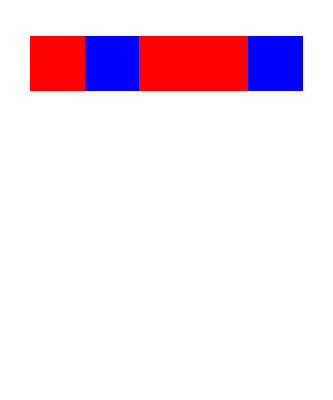
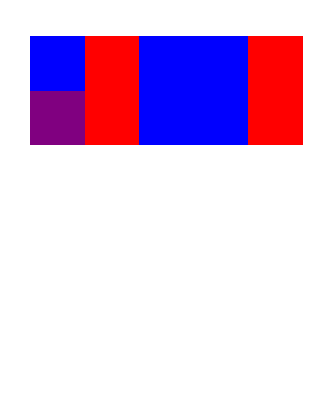
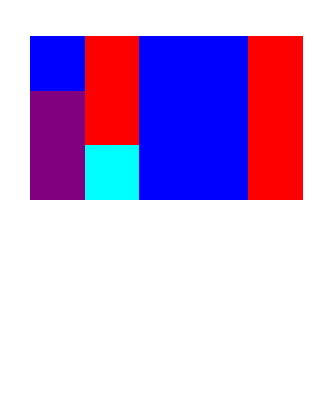
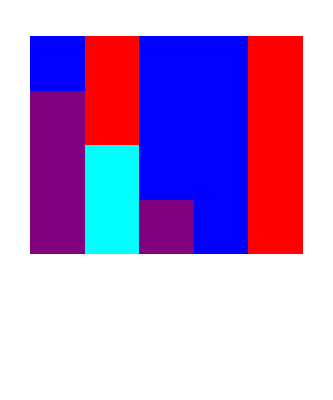
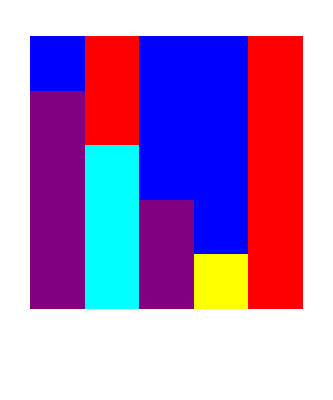
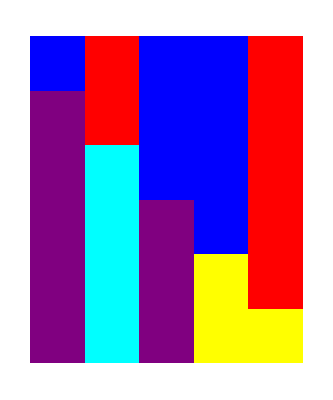

```mathematica
A4[{a,b,a,a,b},
{
{q,p,r},
{{a,a,a,a},{a,a,b,a},{a,b,a,b},{a,b,b,b},{b,a,a,a},{b,a,b,a},{b,b,a,b},{b,b,b,b},{q,q,q,q},{q,q,p,q},{q,q,r,q},{q,p,q,p},{q,p,p,p},{q,p,r,p},{q,r,q,r},{q,r,p,r},{q,r,r,r},{p,q,q,q},{p,q,p,q},{p,q,r,q},{p,p,q,p},{p,p,p,p},{p,p,r,p},{p,r,q,r},{p,r,p,r},{p,r,r,r},{r,q,q,q},{r,q,p,q},{r,q,r,q},{r,p,q,p},{r,p,p,p},{r,p,r,p},{r,r,q,r},{r,r,p,r},{r,r,r,r},{q,a,a,p},{q,a,b,p},{q,b,a,r},{q,b,b,r},{p,b,a,q},{p,b,b,q},{p,a,a,r},{p,a,b,r},{r,a,a,r},{r,a,b,r},{r,b,a,r},{r,b,b,r}},
{r}
}
]
```